# Damped N-tuple Pendulum

## Alexandre Khae Wu Navarro

This notebook executes the symbolic manipulations to obtain the damped n-tuple pendulum equations using the Hamiltonian formalism for dynamical systems.

## System Generation

```mathematica
Clear["Global`*"]
```

Problem parameters:

```mathematica
n = 3;
L = Table[Subscript[l, i],{i, 1, n}];
M = Table[Subscript[m, i],{i, 1, n}];
```

Problem variables:

```mathematica
angles = Table[Subscript[θ, i][t],{i, 1, n}];
dangles = Table[Subscript[θ, i]'[t],{i, 1, n}];
momenta = Table[Subscript[p, i][t],{i, 1, n}];
x = Table[Sum[Subscript[l, i] Sin[Subscript[θ, i][t]],{i, 1, j}],{j, 1, n}];
y = Table[-Sum[Subscript[l, i] Cos[Subscript[θ, i][t]],{i, 1, j}],{j, 1, n}];
dx = D[x,t];
dy = D[y,t];
```

Energy equations and Lagrangian:

```mathematica
T = Sum[g*M[[i]]*y[[i]],{i,1,n}];
V = Sum[1/2 * M[[i]]*(dx[[i]]^2+dy[[i]]^2),{i,1, n}];
Q = Sum[1/2*Subscript[d, i]*Subscript[θ, i]'[t]^2,{i, 1, n}];
Lagrangian = T - (V + Q);
```

Hamiltonian and differential equations for the angles and momentum:
dθ_i/dt=(∂H)/(∂p_i) and dp_i/dt=-(∂H)/(∂θ_i)

```mathematica
pTable=Table[D[Lagrangian,Subscript[θ, i]'[t]],{i,1,n}]//Simplify//Flatten;
Hamiltonian  = Sum[Subscript[p, i][t]*Subscript[θ, i]'[t],{i,1,n}] - Lagrangian;
dthetaTable = Solve[pTable==momenta,dangles]//Simplify//Flatten;
Hamiltonian = Hamiltonian /.dthetaTable;
dpTable = Table[Subscript[p, i]'[t]->-D[Hamiltonian,Subscript[θ, i][t]],{i,1,n}]//Flatten;
system = Union[dthetaTable,dpTable];
(*Some string manipulation to change rule operation to equality*)
systemString = system//FullForm// ToString;
system = StringReplace[systemString, "Rule" -> "Equal"] // ToExpression ;
system//TraditionalForm;
```

## Simulation

Set system parameters to a given value

```mathematica
g =9.8;
valuesL = Table[L[[i]]->5.,{i, 1, n}];
valuesM= Table[M[[i]]->1.,{i, 1, n}];
valuesD= Table[Subscript[d, i]->10.,{i, 1, n}];
parameterValues = Union[valuesL,valuesM,valuesD];
finalTime = 180;
```

```mathematica
odes = system/.parameterValues ;
```

Define boundary conditions

```mathematica
thetaBoundaryValues = Table[π/5 ,{i,1,n}];
dthetaBoundaryValues = Table[0.,{i,1,n}];
thetaBoundaryTable = Table[Subscript[θ, i][0] == thetaBoundaryValues[[i]],{i,1,n}];
momentaThetaBoundary = Table[Subscript[θ, i][t] -> thetaBoundaryValues[[i]],{i,1,n}];
momentaDThetaBoundary = Table[Subscript[θ, i]'[t] -> dthetaBoundaryValues[[i]],{i,1,n}];
pBoundaryValues =pTable/.parameterValues/.momentaThetaBoundary/.momentaDThetaBoundary;
pBoundaryTable = Table[Subscript[p, i][0]==pBoundaryValues[[i]],{i,1,n}];
boundaryConditions = Union[thetaBoundaryTable, pBoundaryTable];
```

Evaluate numerically

```mathematica
variables = Union[Table[Subscript[p, i],{i,1,n}],Table[Subscript[θ, i],{i,1,n}]];
solutions = NDSolve[Union[odes, boundaryConditions],variables,{t, finalTime}];
```

```mathematica
data = Table[Evaluate[angles/.Flatten[solutions]],{t, 0, finalTime, 0.1}];
```

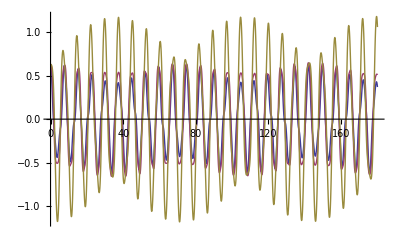

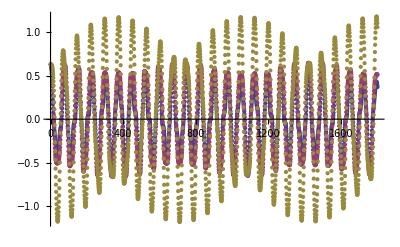

```mathematica
Plot[Evaluate[angles/.solutions],{t,0,finalTime},PlotRange->All]
ListPlot[Transpose[data]]
```

```mathematica
xData=Table[Sum[L[[i]] * Sin[Transpose[data][[i]]]/.valuesL[[i]],{i,1,j}],{j,1,n}];
yData=Table[Sum[-L[[i]] * Cos[Transpose[data][[i]]]/.valuesL[[i]],{i,1,j}],{j,1,n}];
```

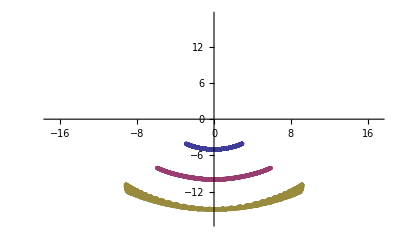

```mathematica
ListPlot[{Transpose[{xData[[1]],yData[[1]]}],Transpose[{xData[[2]],yData[[2]]}],Transpose[{xData[[3]],yData[[3]]}]},PlotRange->{{-17,17},{-17,17}}]
```

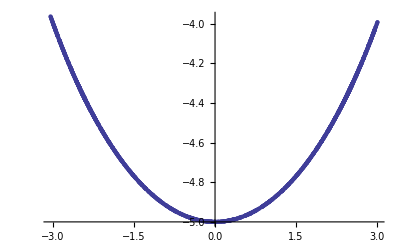

```mathematica
ListPlot[Transpose[{xData[[2]] - xData[[1]],yData[[2]]-yData[[1]]}]]
```

```mathematica
Export["./"<>ToString[n]<>"p_d.csv",Riffle[xData,yData]];
```

Define boundary conditions for Chaotic Pendulum

```mathematica
thetaBoundaryValues = Table[π/2 ,{i,1,n}];
dthetaBoundaryValues = Table[0.,{i,1,n}];
thetaBoundaryTable = Table[Subscript[θ, i][0] == thetaBoundaryValues[[i]],{i,1,n}];
momentaThetaBoundary = Table[Subscript[θ, i][t] -> thetaBoundaryValues[[i]],{i,1,n}];
momentaDThetaBoundary = Table[Subscript[θ, i]'[t] -> dthetaBoundaryValues[[i]],{i,1,n}];
pBoundaryValues =pTable/.parameterValues/.momentaThetaBoundary/.momentaDThetaBoundary;
pBoundaryTable = Table[Subscript[p, i][0]==pBoundaryValues[[i]],{i,1,n}];
boundaryConditions = Union[thetaBoundaryTable, pBoundaryTable];
```

Evaluate numerically

```mathematica
variables = Union[Table[Subscript[p, i],{i,1,n}],Table[Subscript[θ, i],{i,1,n}]];
solutions = NDSolve[Union[odes, boundaryConditions],variables,{t, finalTime}];
```

```mathematica
data = Table[Evaluate[angles/.Flatten[solutions]],{t, 0, finalTime, 0.1}];
```

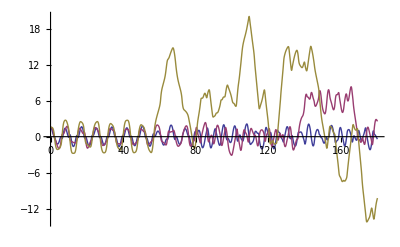

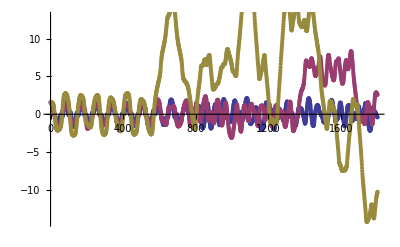

```mathematica
Plot[Evaluate[angles/.solutions],{t,0,finalTime},PlotRange->All]
ListPlot[Transpose[data]]
```

```mathematica
xData=Table[Sum[L[[i]] * Sin[Transpose[data][[i]]]/.valuesL[[i]],{i,1,j}],{j,1,n}];
yData=Table[Sum[-L[[i]] * Cos[Transpose[data][[i]]]/.valuesL[[i]],{i,1,j}],{j,1,n}];
```

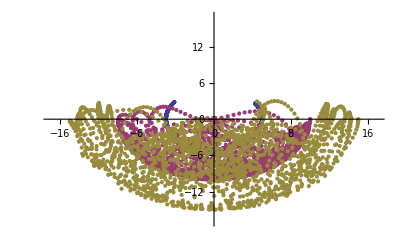

```mathematica
ListPlot[{Transpose[{xData[[1]],yData[[1]]}],Transpose[{xData[[2]],yData[[2]]}],Transpose[{xData[[3]],yData[[3]]}]},PlotRange->{{-17,17},{-17,17}}]
```

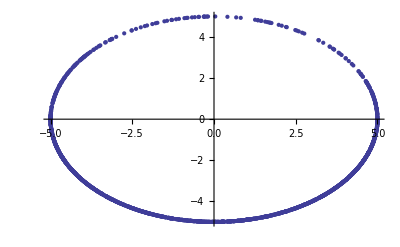

```mathematica
ListPlot[Transpose[{xData[[2]] - xData[[1]],yData[[2]]-yData[[1]]}]]
```

```mathematica
Export["./"<>ToString[n]<>"p_c.csv",Riffle[xData,yData]];
```